```mathematica
α2:=p2/ρ2^γ
α1:=p1/ρ1^γ
rules={
ρ2->(γ+1)/(γ-1+2/M1^2)ρ1,
p2->(2γ M1^2-(γ-1))/(γ+1)p1
};
```

(((1+γ)/(-1+2/M1^2+γ))^-γ (1+(-1+2 M1^2) γ))/(1+γ)

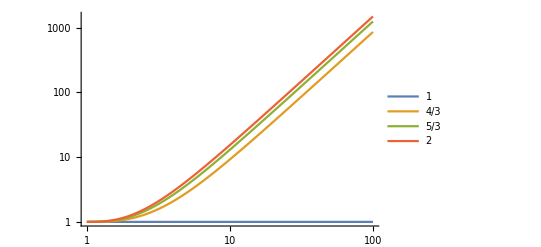

```mathematica
assums={ ρ1>0,γ>0,M1>0};
ratio = Simplify[α2/α1/. rules,assums]
γs = {1,4/3,5/3,2};
LogLogPlot[
Evaluate[ratio/.γ->γs],{M1,1,100},PlotLegends->γs
]
```

```mathematica
massEq:=ρ1 U1==ρ2 U2
momEq:=ρ1 U1^2+p1+B1^2/2==ρ2 U2^2+p2+B2^2/2
energyEq:=(1/2 ρ1 U1^2+f p1+B1^2) U1==(1/2 ρ2 U2^2+f p2 +B2^2) U2
FaradayEq:=B1 U1==B2 U2
eqs={massEq,momEq,energyEq,FaradayEq};
```

```mathematica
rules={
U2->r U1,
f->γ/(γ-1),
B1^2->(U1^2  ρ1)/A^2,
p1->(U1^2  ρ1)/(S^2 γ)
};
Simplify[Eliminate[eqs,{B2,ρ2,p2}]/.rules,{U1>0, ρ1>0}]
```

((-1+r) (S^2 (-2+γ-r γ)+A^2 r (-2+S^2 (1+r-γ+r γ))))/(A S (-1+γ))==0

```mathematica
Collect[S^2 (-2+γ-r γ)+A^2 r (-2+S^2 (1+r-γ+r γ))==0,r]
```

-2 S^2+S^2 γ+r (-2 A^2+A^2 S^2-S^2 γ-A^2 S^2 γ)+r^2 (A^2 S^2+A^2 S^2 γ)==0

```mathematica
Solve[-2 S^2+S^2 γ+r (-2 A^2+A^2 S^2-S^2 γ-A^2 S^2 γ)+r^2 (A^2 S^2+A^2 S^2 γ)==0,{r},Reals,Assumptions->{A>0 ,S>0,γ>0}]//Simplify
```

{{r→(A^2 (2+S^2 (-1+γ))+S^2 γ-√(A^4 (2+S^2 (-1+γ))^2+S^4 γ^2+A^2 (4 S^2 γ+S^4 (8+2 γ-2 γ^2))))/(2 A^2 S^2 (1+γ))},{r→(A^2 (2+S^2 (-1+γ))+S^2 γ+√(A^4 (2+S^2 (-1+γ))^2+S^4 γ^2+A^2 (4 S^2 γ+S^4 (8+2 γ-2 γ^2))))/(2 A^2 S^2 (1+γ))}}

```mathematica
(A^2 (2+S^2 (-1+γ))+S^2 γ+√(A^4 (2+S^2 (-1+γ))^2+S^4 γ^2+A^2 (4 S^2 γ+S^4 (8+2 γ-2 γ^2))))/(2 A^2 S^2 (1+γ))/.{γ->5/3}
```

(3 ((5 S^2)/3+A^2 (2+(2 S^2)/3)+√((25 S^4)/9+A^4 (2+(2 S^2)/3)^2+A^2 ((20 S^2)/3+(52 S^4)/9))))/(16 A^2 S^2)

```mathematica
Plot[(3 ((5 S^2)/3+A^2 (2+(2 S^2)/3)+√((25 S^4)/9+A^4 (2+(2 S^2)/3)^2+A^2 ((20 S^2)/3+(52 S^4)/9))))/(16 A^2 S^2),{A,-2.4431978422951426,2.4431978422951426},{S,-2.2214409457776902,2.2214409457776902}]
```

Plot::nonopt: Options expected (instead of {S,-2.22144,2.22144}) beyond position 2 in Plot[(3 ((5 S^2)/3+A^2 (2+(2 S^2)/3)+√((25 S^4)/9+A^4 Plus[«2»]^2+A^2 (Times[«3»]+Times[«3»]))))/(16 A^2 S^2),{A,-2.4432,2.4432},{S,-2.22144,2.22144}]. An option must be a rule or a list of rules.

Plot[(3 ((5 S^2)/3+A^2 (2+(2 S^2)/3)+√((25 S^4)/9+A^4 (2+(2 S^2)/3)^2+A^2 ((20 S^2)/3+(52 S^4)/9))))/(16 A^2 S^2),{A,-2.4432,2.4432},{S,-2.22144,2.22144}]